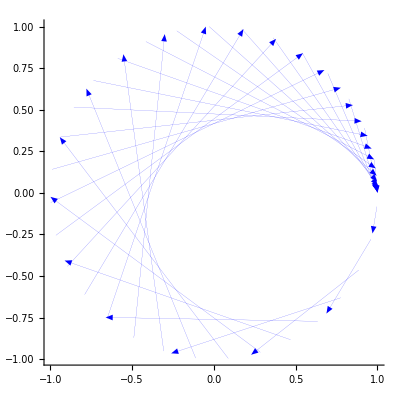

(Cos[t]-Cos[t^3/(4 π^2)]) (-b+Sin[t])+(a-Cos[t]) (Sin[t]-Sin[t^3/(4 π^2)])

a Cos[t]-Cos[t-t^3/(4 π^2)]+b Sin[t]+(3 t^2 ((-a+Cos[t]) Cos[t^3/(4 π^2)]+(-b+Sin[t]) Sin[t^3/(4 π^2)]))/(4 π^2)

```mathematica
ClearAll["Global`*"];
m[t_]:=(Sin[t^3/(4Pi^2)]-Sin[t])/(Cos[t^3/(4Pi^2)]-Cos[t]);
P1[t_]:=(x=Cos[t];y=Sin[t];{x,y});
P2[t_]:=(x=Cos[t^3/(4 π^2)];y=Sin[t^3/(4 π^2)];{x,y});
lines=Table[{P1[t],P2[t]},{t,0*2Pi,1*2Pi,0.2}];
Graphics[{Blue, Thickness[0.0001],Map[Arrow,lines],PlotRange->{{-1,1},{-1,1}},AspectRatio->1},Axes->True]
(* Using equation 16, the two-point form, we obtain the system of equations *)
F[x_,y_,t_]:=(y-P1[t][[2]])(P2[t][[1]]-P1[t][[1]])-(x-P1[t][[1]])(P2[t][[2]]-P1[t][[2]]);
Print[FullSimplify[F[a,b,t]]];
Print[FullSimplify[D[F[a,b,t],t]]];
```

{{u→-(((Cos[t]-Cos[t^3/(4 π^2)]) Sin[t]-Cos[t] (Sin[t]-Sin[t^3/(4 π^2)])) (Sin[t]-(3 t^2 Sin[t^3/(4 π^2)])/(4 π^2))-(-Cos[t]+Cos[t^3/(4 π^2)]) ((3 t^2 Cos[t] Cos[t^3/(4 π^2)])/(4 π^2)-Cos[t-t^3/(4 π^2)]+(3 t^2 Sin[t] Sin[t^3/(4 π^2)])/(4 π^2)))/(-(-Cos[t]+Cos[t^3/(4 π^2)]) (Cos[t]-(3 t^2 Cos[t^3/(4 π^2)])/(4 π^2))+(Sin[t]-Sin[t^3/(4 π^2)]) (Sin[t]-(3 t^2 Sin[t^3/(4 π^2)])/(4 π^2))),v→-((4 π^2 Cos[t] Cos[t^3/(4 π^2)] Sin[t]+3 t^2 Cos[t] Cos[t^3/(4 π^2)] Sin[t]-3 t^2 Cos[t^3/(4 π^2)]^2 Sin[t]-4 π^2 Cos[t-t^3/(4 π^2)] Sin[t]-4 π^2 Cos[t]^2 Sin[t^3/(4 π^2)]+4 π^2 Cos[t-t^3/(4 π^2)] Sin[t^3/(4 π^2)]+3 t^2 Sin[t]^2 Sin[t^3/(4 π^2)]-3 t^2 Sin[t] Sin[t^3/(4 π^2)]^2)/(4 π^2 Cos[t]^2-4 π^2 Cos[t] Cos[t^3/(4 π^2)]-3 t^2 Cos[t] Cos[t^3/(4 π^2)]+3 t^2 Cos[t^3/(4 π^2)]^2+4 π^2 Sin[t]^2-4 π^2 Sin[t] Sin[t^3/(4 π^2)]-3 t^2 Sin[t] Sin[t^3/(4 π^2)]+3 t^2 Sin[t^3/(4 π^2)]^2))}}

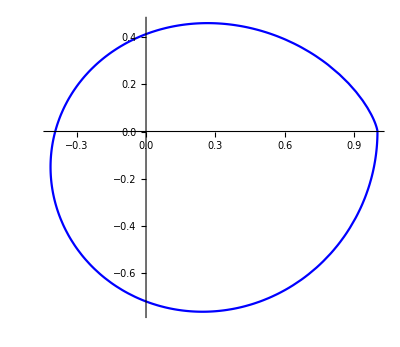

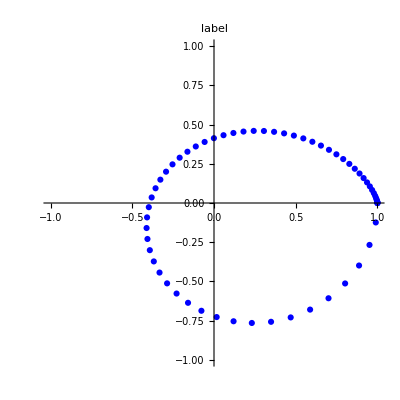

```mathematica
ClearAll["Global`*"];
F[x_,y_,t_]:=(Cos[t]-Cos[t^3/(4 π^2)]) (-y+Sin[t])+(x-Cos[t]) (Sin[t]-Sin[t^3/(4 π^2)]);
Fd[x_,y_,t_]:=x Cos[t]-Cos[t-t^3/(4 π^2)]+y Sin[t]+(3 t^2 ((-x+Cos[t]) Cos[t^3/(4 π^2)]+(-y+Sin[t]) Sin[t^3/(4 π^2)]))/(4 π^2);
(* Retrieve the intersection Points P[u(t),v(t)] *)
Print[Solve[F[u,v,t]==0&&Fd[u,v,t]==0,{u,v}]];
parametricFunc[t_]:={u,v}/.(Solve[F[u,v,t]==0&&Fd[u,v,t]==0,{u,v}]);
ParametricPlot[parametricFunc[t],{t,0.01*2Pi,1*2Pi},PlotStyle->Blue]
(* Full simplifying u(t) and v(t) brings us to this compact form *)
P[t_]=(x=(3 t^2 Cos[t]+4 π^2 Cos[t^3/(4 π^2)])/(4 π^2+3 t^2);y=(3 t^2 Sin[t]+4 π^2 Sin[t^3/(4 π^2)])/(4 π^2+3 t^2);{x,y});
ListPlot[Table[P[t],{t,0*2Pi,1*2Pi,0.1}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label,PlotStyle->Blue]
```